```mathematica
c=299.792458;
m23F=21423.1;
L=6296;
Momt[x_]:=c 9 6.5946(1+x/7500);
β[p_]:=p/(√(m23F^2+p^2));
γ[β_]:=1/(√(1-β^2))
TKE[p_]:=(√(m23F^2+p^2)-m23F)/23
TOF[β_]:=L/(c β);
```

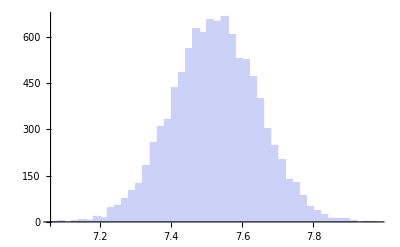

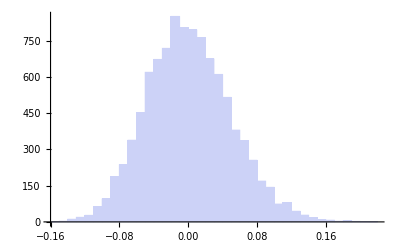

```mathematica
listTOF=RandomVariate[NormalDistribution[7.52,0.12],10000];
Histogram[listTOF]
KKK=Table[TKE[m23F γ[1457/(c listTOF[[i]])] 1457/(c listTOF[[i]])]/TKE[m23F γ[1457/(c 7.52)] 1457/(c 7.52)]-1,{i,1,10000}];
(*KKK=Table[TKE[m23F γ[1457/(c listTOF[[i]])] 1457/(c listTOF[[i]])],{i,1,10000}];*)
Histogram[KKK]
```

```mathematica
TKE[Momt[0]]
TKE[Momt[20]]
TKE[Momt[20]]-TKE[Momt[0]]
```

279.369

280.688

1.31912

```mathematica
TOF[β[Momt[0]]]
TOF[β[Momt[20]]]
TOF[β[Momt[0]]]-TOF[β[Momt[20]]]
```

32.8697

32.818

0.0517047

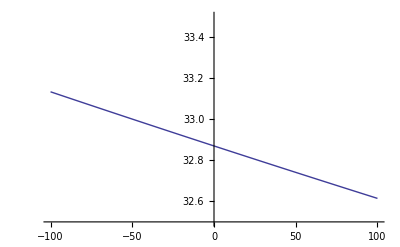

```mathematica
Plot[TOF[β[Momt[x]]],{x,-100,100},PlotRange->{32.5, 33.5}]
```